## Metodo semiserio

Si può automatizzare la ricerca della biforcazione. Per determinare la biforcazione n-esima, si parte da un appropriato valore di μ inferiore a quello di biforcazione (stimato ad occhio) e si confrontano, per un N opportunamente grande, le iterate N-esima e (N+2^n)-esima di uno stesso punto inziale. Se sono molto vicini, non siamo ancora alla biforcazione, e bisogna aumentare μ. Appena cominciano ad allontanarsi, siamo arrivati alla biforcazione.

### Codice

```mathematica
ClearAll["Global`*"]
```

```mathematica
f[μ_,x_]:= μ x(1-x)
fn=Compile[{{μ,_Real},{x,_Real},{n,_Integer}},Nest[f[μ,#]&,x,n]];
dist[μ_,x0_,Ν_,n_]:=Abs[fn[μ,x0,Ν]-fn[μ,x0,Ν+2^n]]
indagine[n_,x0_,Ν_,{min_,max_,step_}]:=ParallelTable[{μ,dist[μ,x0,Ν,n]},{μ,min,max,step}]
indaginePlot[n_,x0_,Ν_,{min_,max_,step_}]:=ListPlot[indagine[n,x0,Ν,{min,max,step}],AspectRatio->1,PlotRange->Full]
sospetto[n_,x0_,Ν_,{min_,max_,step_}]:=Module[
{
ind=indagine[n,x0,Ν,{min,max,step}],
val,
spike
},
val=Last/@ind;
spike=Max@val;
Cases[ind,{_,spike}]
]
colpevole[n_,x0_,Ν_,{min_,max_,step_}]:=sospetto[n,x0,Ν,{min,max,step}]⟦1,1⟧
```

### Test

#### Biforcazione a μ_1=3

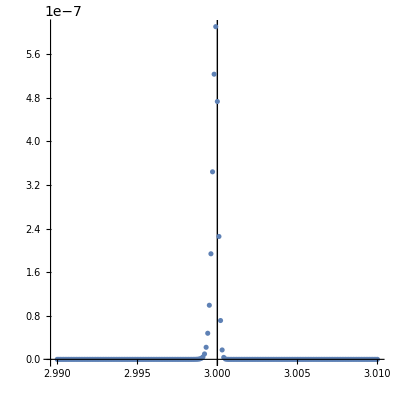

```mathematica
ListPlot[indagine[2,0.4,10^4,{2.99,3.01,10^-4}],AspectRatio->1,PlotRange->Full,Epilog->{InfiniteLine[{{3,0},{3,1}}]}]
```

#### Biforcazione a μ_2=1+√6

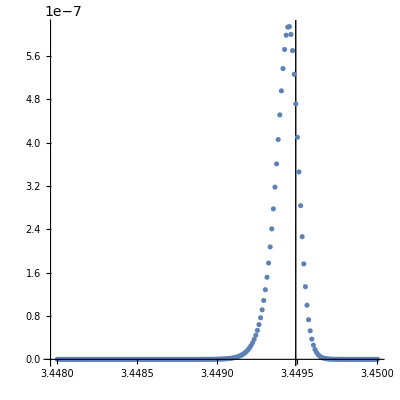

```mathematica
ListPlot[indagine[3,0.4,10^4,{3.448,3.45,10^-5}],AspectRatio->1,PlotRange->Full,Epilog->{InfiniteLine[{{1+√6,0},{1+√6,1}}]}]
```

```mathematica
(1+√6-3.4494459999999996)/(1+√6)
```

0.0000126809

Quindi non solo il metodo pare funzionare, ma gli errori numerici che compie potrebbero essere inferiori all’1%! Godo.

#### Altre biforcazioni

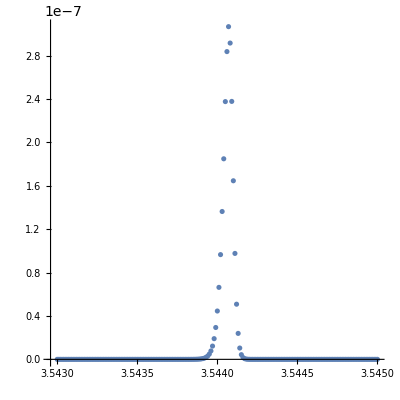

```mathematica
ListPlot[indagine[4,0.4,10^4,{3.543,3.545,10^-5}],AspectRatio->1,PlotRange->Full]
```

```mathematica
sospetto[4,0.4,10^4,{3.54,3.55,10^-5}]
```

{{3.54407,3.06786×10^-7}}

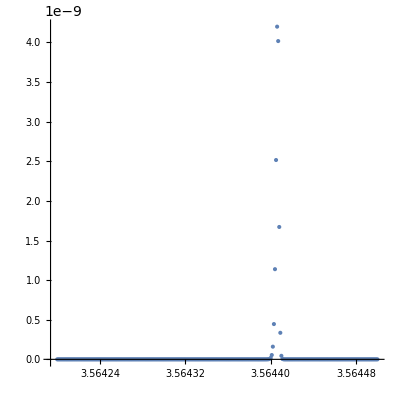

```mathematica
indaginePlot[5,0.4,10^5,{3.5642,3.5645,10^-6}]
```

```mathematica
sospetto[5,0.4,10^5,{3.56439,3.56441,10^-7}]
```

{{3.56441,4.50185×10^-9}}

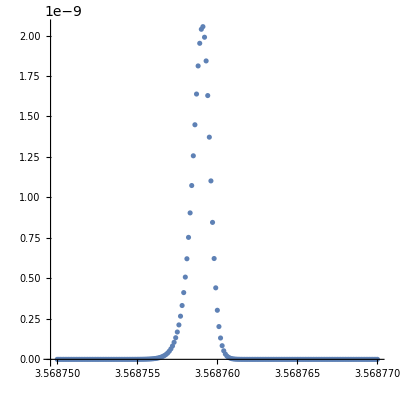

```mathematica
indaginePlot[6,0.4,10^5,{3.56875,3.56877,10^-7}]
```

```mathematica
sospetto[6,0.4,10^5,{3.5687,3.5688,10^-7}]
```

{{3.56876,2.05492×10^-9}}

```mathematica
NumberForm[%,10]
```

{{3.5687591,2.054920345×10^-9}}

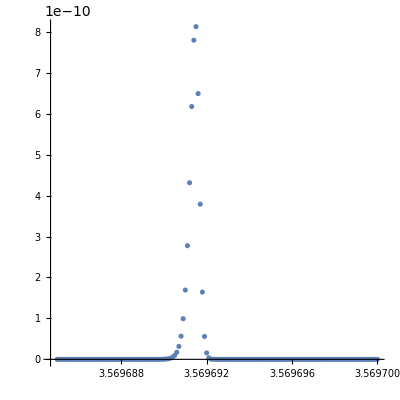

```mathematica
indaginePlot[7,0.4,10^5,{3.569685,3.5697,10^-7}]
```

```mathematica
sospetto[7,0.4,10^5,{3.569685,3.5697,10^-7}]
```

{{3.56969,8.12949×10^-10}}

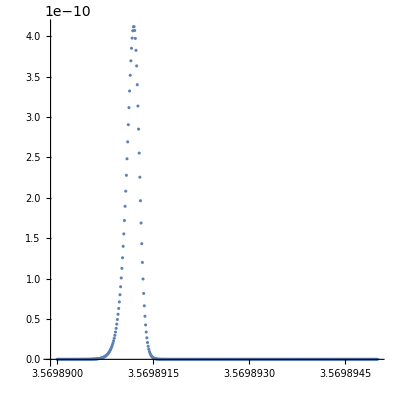

```mathematica
indaginePlot[8,0.4,10^5,{3.56989,3.569895,10^-8}]
```

```mathematica
sospetto[8,0.4,10^5,{3.569885,3.569895,10^-8}]
```

{{3.56989,4.11764×10^-10}}

```mathematica
NumberForm[%,15]
```

{{3.5698912,4.11764011776228×10^-10}}

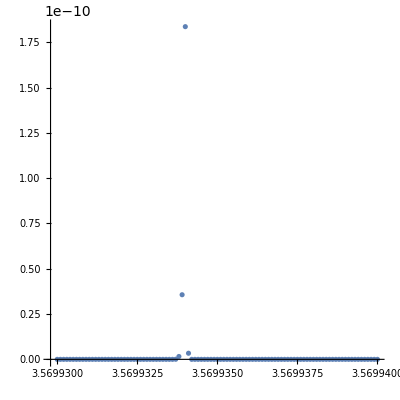

```mathematica
indaginePlot[9,0.4,10^5,{3.56993,3.56994,10^-7}]
```

```mathematica
sospetto[9,0.4,10^5,{3.56993,3.56994,10^-8}]
```

{{3.56993,1.8708×10^-10}}

```mathematica
NumberForm[%,10]
```

{{3.56993399,1.870799626×10^-10}}

### Conseguenze

```mathematica
biforcazioni={
3.,
1.+√6,
colpevole[4,0.4,10^4,{3.54,3.55,10^-5}],
colpevole[5,0.4,10^5,{3.56439,3.56441,10^-7}],
colpevole[6,0.4,10^5,{3.5687,3.5688,10^-7}],
colpevole[7,0.4,10^5,{3.569685,3.5697,10^-7}],
colpevole[8,0.4,10^5,{3.569885,3.569895,10^-8}],
colpevole[9,0.4,10^5,{3.56993,3.56994,10^-8}]
}
```

{3.,3.44949,3.54407,3.56441,3.56876,3.56969,3.56989,3.56993}

```mathematica
rapporti=Table[(biforcazioni[[n]]-biforcazioni[[n-1]])/(biforcazioni[[n+1]]-biforcazioni[[n]]),{n,2,7}]
```

{4.75247,4.65076,4.67226,4.66817,4.669,4.66698}

```mathematica
coefficiente=rapporti//Last;
```

```mathematica
NumberForm[coefficiente,20]
```

4.666978265979232

```mathematica
nuovaBiforcazione[n_Integer]:=nuovaBiforcazione[n]=Piecewise[{{biforcazioni[[n]], n≤8}, {(nuovaBiforcazione[n-1]-nuovaBiforcazione[n-2])/coefficiente+nuovaBiforcazione[n-1], n>8}}]
```

```mathematica
NumberForm[nuovaBiforcazione/@Range[75],50]
```

{3.,3.449489742783178,3.54407,3.5644065,3.5687591,3.5696915,3.5698912,3.56993399,3.56994315867351,3.569945123258085,3.569945544212386,3.569945634410856,3.56994565373781,3.569945657879023,3.569945658766367,3.569945658956499,3.569945658997239,3.569945659005969,3.569945659007839,3.56994565900824,3.569945659008326,3.569945659008344,3.569945659008348,3.569945659008349,3.569945659008349,3.569945659008349,3.569945659008349,3.569945659008349,3.569945659008349,3.569945659008349,3.569945659008349,3.569945659008349,3.569945659008349,3.569945659008349,3.569945659008349,3.569945659008349,3.569945659008349,3.569945659008349,3.569945659008349,3.569945659008349,3.569945659008349,3.569945659008349,3.569945659008349,3.569945659008349,3.569945659008349,3.569945659008349,3.569945659008349,3.569945659008349,3.569945659008349,3.569945659008349,3.569945659008349,3.569945659008349,3.569945659008349,3.569945659008349,3.569945659008349,3.569945659008349,3.569945659008349,3.569945659008349,3.569945659008349,3.569945659008349,3.569945659008349,3.569945659008349,3.569945659008349,3.569945659008349,3.569945659008349,3.569945659008349,3.569945659008349,3.569945659008349,3.569945659008349,3.569945659008349,3.569945659008349,3.569945659008349,3.569945659008349,3.569945659008349,3.569945659008349}

## Delirio totale

```mathematica
NonlinearModelFit[Transpose[{Range[-1,8],{0,1,3,1+√6,3.5440903,3.5644073,3.5687594,3.5696916,3.5698913,3.5699340}}],-Exp[b x]+c,{b,c},x]
```

FittedModel[3.36316-ⅇ^(-1.21614 x)]

```mathematica
Interpolation[Transpose[{Range[0,8],{1,3,1+√6,3.5440903,3.5644073,3.5687594,3.5696916,3.5698913,3.5699340}}]]
```

InterpolatingFunction[…]

```mathematica
Manipulate[Plot[{3.5699456718709449018420051513864989367638369115148323781079755299213628875001367775263210342163-2.853 ⅇ^(-α x)},{x,1,10},PlotRange->Full,Epilog->{Thick,Point/@({Range[8],{3,1+√6,3.5440903,3.5644073,3.5687594,3.5696916,3.5698913,3.5699340}}ᵀ)}],{α,1.5,1.6}]
```

```mathematica
Log[2.853 ]
```

1.04837

```mathematica
g[x_]:=3.5699456718709449018420051513864989367638369115148323781079755299213628875001367775263210342163-28530/10000 ⅇ^(-1.5409880955x);
NumberForm[Limit[(g[n-1]-g[n-2])/(g[n]-g[n-1]),n->Infinity],20]
```

4.669201609490461

```mathematica
(g/@Range[8]-{3,1+√6,3.5440903,3.5644073,3.5687594,3.5696916,3.5698913,3.5699340})/{3,1+√6,3.5440903,3.5644073,3.5687594,3.5696916,3.5698913,3.5699340}//Abs//Log10
```

{-1.8635,-2.52043,-3.21275,-3.88536,-4.55567,-5.2252,-5.89043,-6.5718}

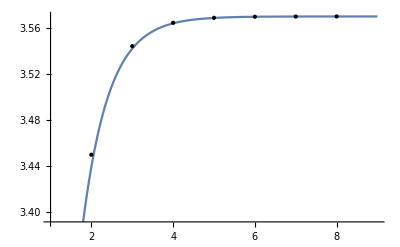

```mathematica
Plot[g[x],{x,1,9},Epilog->{Thick,Point/@Transpose[{Range[8],{3,1+√6,3.5440903,3.5644073,3.5687594,3.5696916,3.5698913,3.5699340}}]}]
```

## Diagramma con f_μ^n contro μ (l’ho perso)

```mathematica
Manipulate[Plot[{fn[μ,x,n],x},{x,0,1},AspectRatio->1,Ticks->Table[Range[0,1,.1],2],PlotPoints->5000],{{μ,2.2},0,4},{n,2^Range[0,5]}]
```

```mathematica
Series[fn[μ,x,16],{x,1/2,2}]/.μ->3.55
```

0.505483+5.80676×10^70 (x-1/2)^2+O[x-1/2]^3